Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ℏωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
hbarraomegaAu=Drop[ℏωAu,{1,2}];
epsReal=Re[Drop[nAu,{1,2}]^2];
epsImag=Im[Drop[nAu,{1,2}]^2];
```

```mathematica
auReal = Interpolation[Transpose[{hbarraomegaAu,epsReal}]];
auImag = Interpolation[Transpose[{hbarraomegaAu,epsImag}]];
```

```mathematica
h c/5
```

248.14

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

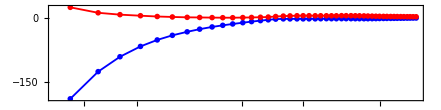

```mathematica
drudeAu=ListLogLinearPlot[{Style[auReal ,Blue],Style[auImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.2],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.2]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeAu.svg",drudeAu]
```

drudeAu.svg

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h c/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
hbarraomegaAg0=Drop[ℏωAg,{1,20}];
hbarraomegaAg=Drop[hbarraomegaAg0,{-13,-1}];
nAggg=Drop[nAgg,{1,20}];
epsRealAg=1-Re[Drop[nAggg,{-13,-1}]^2];
epsImagAg=Im[Drop[nAggg,{-13,-1}]^2];
```

```mathematica
hbarraomegaAg
```

{4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158}

```mathematica
agReal = Transpose[{hbarraomegaAg,epsRealAg}];
agImag = Transpose[{hbarraomegaAg,epsImagAg}];
```

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

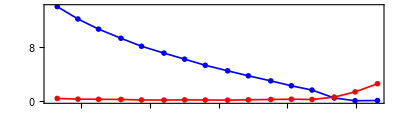

```mathematica
drudeAg=ListPlot[{Style[agReal ,Blue],Style[agImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/3.5]
```

```mathematica
Export["drudeAg.svg",drudeAg]
```

drudeAg.svg

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
bism=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

Import::nffil: File C:\Users\Lunita\OneDrive\Documentos\GitHub\Servicio-Social\Notebooks Mathematica\Funciones dieléctricas\Bismuto Hagemann.csv not found during Import.

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
ℏωBism=h c/λBism; (*eV*)
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
λBism
```

{0.00248,0.004133,0.0124,0.01378,0.01459,0.0248,0.04133,0.06199,0.08266,0.08856,0.09537,0.1033,0.124,0.155,0.2066,0.31,0.3542,0.3757,0.3875,0.3999,0.4133,0.4428,0.4769,0.4959,0.5061,0.5166,0.5636,0.6199,0.6888,0.7749,0.8856,0.9537,1.033,1.127,1.24,1.305,1.378,1.459,1.55,1.653,1.771,1.907,2.066,2.254,2.48,2.583,2.695,2.818,2.952,3.1,3.179,3.263,3.351,3.444,3.542,3.647,3.757,3.875,3.999,4.133,4.275,4.428,4.592,4.769,4.959,5.166,5.391,5.636,5.904,6.199,6.525,6.888,7.293,7.749,8.266,8.551,8.856,9.184,9.537,9.919,10.33,10.78,11.27,11.81,12.4,13.05,13.78,14.59,15.5,16.53,17.71,19.07,20.66,21.01,21.38,21.75,22.14,22.54,22.96,23.39,23.84,24.31,24.8,25.83,26.95,28.18,29.52,31.,32.63,34.44,36.47,37.57,38.75,39.99,41.33,42.03,42.75,43.5,44.28,45.09,45.92,46.79,47.69,48.62,49.59,50.61,51.66,52.76,53.91,56.36,61.99,68.88,77.49,88.56,103.3,124.,155.,206.6,248.,310.,354.2,413.3,495.9,619.9,826.6,1240.,1550.,2066.,3100.,6199.}

```mathematica
lambdaBi=Drop[Drop[λBism,{1,139}],{-3,-1}]
```

{310.,354.2,413.3,495.9,619.9,826.6,1240.,1550.}

```mathematica
hbarraomegaBi=Drop[Drop[ℏωBism,{1,139}],{-3,-1}]
epsRealBi=Drop[Re[Drop[nBismuto,{1,139}]^2],{-3,-1}];
epsImagBi=Drop[Im[Drop[nBismuto,{1,139}]^2],{-3,-1}];
```

{4.00226,3.50282,3.00194,2.50192,2.00145,1.50097,1.00056,0.800452}

```mathematica
biReal = Interpolation[Transpose[{hbarraomegaBi,epsRealBi}]];
biImag = Interpolation[Transpose[{hbarraomegaBi,epsImagBi}]];
```

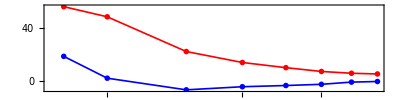

```mathematica
drudeBi=ListLogLinearPlot[{Style[biReal ,Blue],Style[biImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
h c/1.2
```

1033.92

```mathematica
Export["drudeBi.svg",drudeBi]
```

drudeBi.svg

```mathematica
h c/(5*10^(8))
```

2.4814×10^-6

```mathematica
upperTicks4=Module[{labels,positions},labels={2.5*^-6,3.1*^-6,4.1*^-6,6.2*^-6,1.24*10^(-5)};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

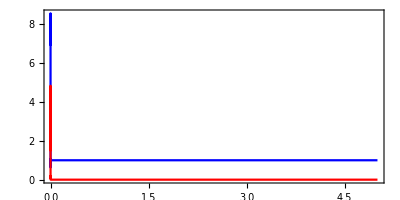

```mathematica
bis=ListLinePlot[{Style[Transpose[{ℏωBism,nBis}],Blue],Style[Transpose[{ℏωBism,kBis}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["Bisexp.svg",bis]
```

Bisexp.svg

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000;(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
λMgO
```

{360.,410.4,460.8,511.2,561.6,612.,662.4,712.8,763.2,813.6,864.,914.4,964.8,1015.,1066.,1116.,1166.,1217.,1267.,1318.,1368.,1418.,1469.,1519.,1570.,1620.,1670.,1721.,1771.,1822.,1872.,1922.,1973.,2023.,2074.,2124.,2174.,2225.,2275.,2326.,2376.,2426.,2477.,2527.,2578.,2628.,2678.,2729.,2779.,2830.,2880.,2930.,2981.,3031.,3082.,3132.,3182.,3233.,3283.,3334.,3384.,3434.,3485.,3535.,3586.,3636.,3686.,3737.,3787.,3838.,3888.,3938.,3989.,4039.,4090.,4140.,4190.,4241.,4291.,4342.,4392.,4442.,4493.,4543.,4594.,4644.,4694.,4745.,4795.,4846.,4896.,4946.,4997.,5047.,5098.,5148.,5198.,5249.,5299.,5350.,5400.}

```mathematica
hbarraomegaMgO=Drop[ℏωMgO,{-95,-1}];
epsRealMgO=1-Re[Drop[nMgO,{-95,-1}]^2];
epsImagMgO=Im[Drop[nMgO,{-95,-1}]^2];
```

```mathematica
mgOReal = Interpolation[Transpose[{hbarraomegaMgO,epsRealMgO}]];
mgOImag = Interpolation[Transpose[{hbarraomegaMgO,epsImagMgO}]];
```

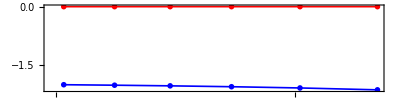

```mathematica
drudeMgO=ListLogLinearPlot[{Style[mgOReal ,Blue],Style[mgOImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export["drudeMgO.svg",drudeMgO]
```

drudeMgO.svg

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

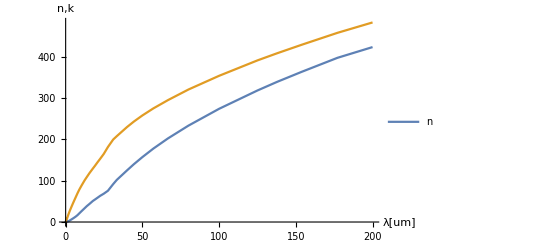

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

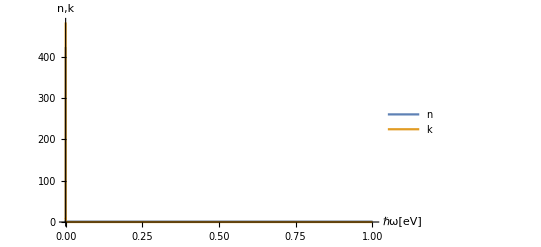

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

```mathematica
h c/350
```

3.54486

```mathematica
ϵℏω[ℏω_,ℏωp_,ℏγ_]:=1-((ℏωp/ℏ)^2/((ℏω/ℏ)((ℏω/ℏ)+ I * (ℏγ/ℏ))))(*recibe en eV*)
```

```mathematica
alReal=Table[{ℏω,1-Re[ϵℏω[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
alImag=Table[{ℏω,Im[ϵℏω[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
```

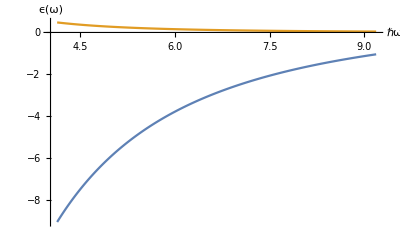

```mathematica
ListLinePlot[{alReal,alImag},AxesLabel->{"ℏω","ϵ(ω)"}]
```

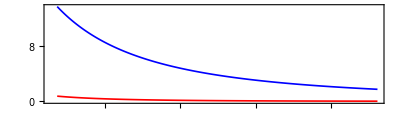

```mathematica
drudeAl=ListPlot[{Style[alReal ,Blue],Style[alImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",13],Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.2],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.2],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/3.5]
```

```mathematica
Export["drudeAl.svg",drudeAl]
```

drudeAl.svg